```mathematica
SetDirectory[NotebookDirectory[]]
Kann[a_]:=(

(*taking in data in erg/cm2/s*)
c={};
b=Import[a,"Table"];
For[i=1,b[[i,2]]!="photon",i++,];
c=Take[b,i-1];
table={};
data={};
Do[
If[Head[c[[i,1]]]==Real,{

time=c[[i,1]];
beta=c⟦i,5⟧;
z=c⟦i,6⟧;

(*remember, Block 1 is in obs frame, need to correct to rest frame*)
If[time>0,
time=time/(1+z);
logtime=Log[10,time];

flux=c⟦i,2⟧/(1+z)^(1-beta);
fluxposerr=c⟦i,3⟧/(1+z)^(1-beta);
fluxnegerr=c⟦i,4⟧/(1+z)^(1-beta);


logflux=Log[10,flux];
logfluxerror=((fluxposerr+fluxnegerr)/2)/(flux*Log[10]);

If[flux>0,AppendTo[table,{logtime,logflux,logfluxerror}]];
If[flux>0,AppendTo[data,{logtime,logflux}]];
]}
]
,{i,1,Length[c]}];

Kanndata=data;
Return[Kanndata];
)
```

C:\Users\Maura Tapia\Documents\Dr. Dainotti GRB Poland\Combined light curves\Combining_Li_Liang\PR combination files Aug10\PR combination files Aug10

```mathematica
(*needs to be called with the redshift and beta values*)
Liang[a_, beta_,z_]:=(

(*taking in data in erg/cm2/s I think!*)
c={};
b=Import[a,"Table"];
For[i=1,b[[i,2]]!="photon",i++,];
c=Take[b,i-1];
table={};
data={};
Do[
If[Head[c[[i,1]]]==Real,{

time=c[[i,1]]+100;

(*remember, data is in obs frame, need to correct to rest frame*)
If[time>0,
time=time/(1+z);
logtime=Log[10,time];

flux=c⟦i,2⟧/(1+z)^(1-beta);
fluxerr=c⟦i,3⟧/(1+z)^(1-beta);


logflux=Log[10,flux];
logfluxerror=fluxerr/(flux*Log[10]);

If[flux>0,AppendTo[table,{logtime,logflux,fluxerr}]];
If[flux>0,AppendTo[data,{logtime,logflux}]];
]}
]
,{i,1,Length[c]}];

Liangdata=table;
Return[Liangdata];
)
```

```mathematica
(*Divisions = dzielenie, so binning?*)
Dzielenie[start_,end_]:= (*beginning of plateau emission, where you start and end the curve-fitting*)
(
startp=start ;
endp=end;
Part1={};
Δt1={};
ΔF1={};
Part2={};
Δt2={};
ΔF2={};

(*I think this is how the program cuts out points outside of [tt,tf]*)
Do[If[startp≤dane[[i,1]]≤endp,
(
AppendTo[Part1,dane[[i]]];
AppendTo[Δt1,Δt[[i]]];
AppendTo[ΔF1,ΔF[[i]]];
),
(
AppendTo[Part2,dane[[i]]];
AppendTo[Δt2,Δt[[i]]];
AppendTo[ΔF2,ΔF[[i]]];
)
],{i,1,Length[dane]}];
);
```

```mathematica
(*Willingale function*)
model[F_,T_,α_,t_]:=Piecewise[{{Log[10,10^F*Exp[α-(10^x*α/10^T)]*Exp[-Abs[t]/10^x]],10^x<10^T},{Log[10,10^F*(10^x/10^T)^(-α)*Exp[-Abs[t]/10^x]],10^x≥10^T}}];
```

```mathematica
(*Fitting = fitowanie*)
fitowanie[a_,b_,c_,d_,er_,datapart_,beg_,end_]:=
(fit1=NonlinearModelFit[datapart,model[F,T,α,t],{{F,a},{T,b},{α,c},{t,d}},x,Weights->1/er^2];
bestparameters=fit1["BestFitParameters"];
besterrors=fit1["ParameterErrors"];
Print["----------------------------------------------"];
Print["best fit parameters: ",bestparameters];
Print["theirs errors: ",besterrors];
Print["confidence intervals: ",fit1["ParameterConfidenceIntervals",ConfidenceLevel->0.68]];


(*if Subscript[t, a] is <0 we have to fix it and refit in order for following Δχ^2 calculations*)
If[fit1["BestFitParameters"][[4,2]]≤0,
(
Clear[bestparameters];
startowe={{F,a},{T,b},{α,c}};
fit1=NonlinearModelFit[datapart,model[F,T,α,0],startowe,x,Weights->1/er^2]; (*this line has t=0*)
bestparameters=fit1["BestFitParameters"];
besterrors=fit1["ParameterErrors"];
zamiana[i_,k_]:={parametr[[i]]->FaTaTable[[i,k]],t->0};
start={{F,#[[1,2]]},{T,#[[2,2]]},{α,#[[3,2]]}}&[bestparameters];
Flux=model[F,T,α,0]/.bestparameters;
Print["!!!!!!!!!!!!!!!!!!! changing best fit parameters to: ",bestparameters," with fixed ta->0"];
Print["best fit parameters: ",bestparameters];
Print["theirs errors: ",besterrors];
Print["confidency intervals: ",fit1["ParameterConfidenceIntervals",ConfidenceLevel->0.68]];
),
(
zamiana[i_,k_]:={parametr[[i]]->FaTaTable[[i,k]]};
start={{F,#[[1,2]]},{T,#[[2,2]]},{α,#[[3,2]]},{t,#[[4,2]]}}&[bestparameters];
Flux=model[F,T,α,t]/.bestparameters
)
];
Print[
Show[
Plot[model[F,T,α,t]/.bestparameters/.t->0,{x,beg,end}],ListPlot[datapart,PlotRange->All],ListPlot[{{bestparameters[[2]][[2]],bestparameters[[1]][[2]]}},PlotStyle->{Green, PointSize[0.05]},PlotRange->All],
PlotRange->All,FrameLabel->{"log time rest frame (s)","log Flux (erg s^-1)"}]]
Print["----------------------------------------------"];
Clear[fit1];
)
```

```mathematica
(*Cutting = wycinanie*)
Wycinanie[a_,b_]:=
(
przedziałT:=Interval[{a[[1]],b[[1]]}]; (*compartments = bins?*)
przedziałF:=Interval[{a[[2]],b[[2]]}];
Do[
If[!IntervalMemberQ[przedziałT,dane[[i,1]]]||!IntervalMemberQ[przedziałF,dane[[i,2]]],
(
AppendTo[Part12,dane[[i]]];
AppendTo[Δt12,Δt[[i]]];
AppendTo[ΔF12,ΔF[[i]]];
)
];
,{i,1,Length[dane]}];

dane=Part12;
Δt=Δt12;
ΔF=ΔF12;

Part12={};
Δt12={};
ΔF12={};
)
```

```mathematica
Chisquare[datapart_,er_]:=Module[{ν,REDUCED},


singleχ[j_]:=((datapart[[All,2]]-Flux/.x->datapart[[All,1]])/er[[All]])^2;

bestfitχ=Sum[singleχ[All],{All,1,Length[datapart]}];
REDUCED=bestfitχ/(Length[datapart]-3);
ν=Length[datapart];
X=REDUCED ν;
PROBABILITY=(2^(-ν/2) /Gamma[ν/2])NIntegrate[ⅇ^(-x/2) x^(-1+ν/2),{x,X,Infinity}];
Print["GRB ",id," afterglow has"," χ^2: ",bestfitχ," and  reduced χ^2: ",REDUCED," α: ",Chop[PROBABILITY]];
];
```

```mathematica
IntervalEstimating[b_,e_,s_,datapart_,er_]:=
(
Print["--------------testing-------------"];
FaTaTable={};

parametr=Table[bestparameters[[i,1]],{i,1,3}];
bestparam=Table[bestparameters[[i,2]],{i,1,3}];
errors=Table[besterrors[[i]],{i,1,3}];

beg=b;                                             (*flexible interval for error multiplier*)
end=e;
step=s;
multiplier=Sort[Join[Table[-end+i step,{i,0,(end-beg)/step}],Table[beg+i step,{i,0,(end-beg)/step}]]];
Do[
values=Table[bestparam[[j]]+multiplier[[i]]*errors[[j]],{i,1,Length[multiplier]}];
AppendTo[FaTaTable,values]
,{j,1,3}];

quantity=2 ((end-beg)/step+1);

Print["---------------------------------"];

(*******  main ugly loop for Δχ^2 calculations :) ********)
Clear[Flux1];
singleχ[j_]:=((1/er[[j]])(datapart[[j,2]]-Flux1/.x->datapart[[j,1]]))^2;
Δtable={{},{},{},{}};
finaltable={};
Print["---------------------------------"];
Do[

Do[
parametry=Drop[start,{i}];

fit12=NonlinearModelFit[datapart,model[F,T,α,t]/.zamiana[i,k],parametry,x,Weights->1/er^2];

Clear[χsquare,Flux1];
Flux1=model[F,T,α,t]/.fit12["BestFitParameters"]/.zamiana[i,k];
χsquare=Sum[singleχ[j],{j,1,Length[datapart]}];
Δχ=χsquare-bestfitχ;

AppendTo[Δtable[[i]],{multiplier[[k]],Chop[Δχ]}];

(*Print[Row[{"σ x ",multiplier[[k]],"   ","Δχ:",Chop[Δχ],"   ",zamiana[i,k],"  ",χsquare," ",fit12["BestFitParameters"]}]] ;*)
(*checking tool{set "i" for one value}*)
,{k,1,quantity}];


Clear[left,right,leftm,rightm];
left=Drop[Δtable[[i]],(-Length[Δtable[[i]]])/2];
right=Drop[Δtable[[i]],Length[Δtable[[i]]]/2];

Do[
(*Print[left[[t,2]],">3.5>",left[[t+1,2]]," ",left[[t,2]]≥3.5≥left[[t+1,2]]];*)
If[left[[t,2]]≥1≥left[[t+1,2]],leftm=((left[[t+1,1]]-left[[t,1]])(1-left[[t,2]]))/(left[[t+1,2]]-left[[t,2]])-left[[t,1]]];
If[right[[t,2]]≤1≤right[[t+1,2]],rightm=((right[[t+1,1]]-right[[t,1]])(1-right[[t,2]]))/(right[[t+1,2]]-right[[t,2]])-right[[t,1]]];
,{t,1,Length[Δtable[[i]]]/2-1}];
Print[leftm," ",rightm];
AppendTo[finaltable,
{bestparameters[[i,1]],
bestparameters[[i,2]],
(Sort[{If[NumericQ[leftm],bestparameters[[i,2]]+leftm besterrors[[i]],"error"],If[NumericQ[rightm],bestparameters[[i,2]]+rightm besterrors[[i]],"error"]}])}];

Clear[leftm,rightm];
,{i,1,3}];
(*parameters*)

Print[
TableForm[
Table[{finaltable[[i,1]],finaltable[[i,2]],"("<>ToString[finaltable[[i,3,1]]]<>" ,",ToString[finaltable[[i,3,2]]]<>")"},{i,1,3}]
,TableHeadings->{None,{"parameter","best fit"," confidency","interval"}}]];

Print[Row[Table[ListPlot[Δtable[[i]],PlotRange->All,ImageSize->Medium,PlotLabel->ToString[parametr[[i]]],FrameLabel->{"σ multiplier","Δχ^2"},Axes->False,Frame->True]
,{i,1,3}]]];

Print["---------------------------------"];
);
```

Part::partw: Part 6 of Kann[060418_Kann.txt] does not exist.

Part::partw: Part 4 of Liang[060418_Liang.txt,0.69,1.4901] does not exist.

Part::partd: Part specification Liang[060418_Liang.txt,0.69,1.4901]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification Liang[060418_Liang.txt,0.69,1.4901]⟦All,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Liang[060418_Liang.txt,0.69,1.4901]⟦All,1⟧,Log[10^(Kann[060418_Kann.txt]⟦6,2⟧-Liang[«3»]⟦4,2⟧+Liang[060418_Liang.txt,0.69,1.4901]⟦All,2⟧)]/Log[10]} cannot be transposed.

Part::partd: Part specification Liang[060418_Liang.txt,0.69,1.4901]⟦All,1⟧ is longer than depth of object.

Part::partd: Part specification Liang[060418_Liang.txt,0.69,1.4901]⟦All,3⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {10^(Liang[060418_Liang.txt,0.69,1.4901]⟦All,1⟧),10^(Kann[060418_Kann.txt]⟦6,2⟧-Liang[060418_Liang.txt,0.69,1.4901]⟦4,2⟧+Liang[060418_Liang.txt,0.69,1.4901]⟦All,2⟧),Liang[060418_Liang.txt,0.69,1.4901]⟦All,3⟧} cannot be transposed.

Transpose[{10^(Liang[060418_Liang.txt,0.69,1.4901]⟦All,1⟧),10^(Kann[060418_Kann.txt]⟦6,2⟧-Liang[060418_Liang.txt,0.69,1.4901]⟦4,2⟧+Liang[060418_Liang.txt,0.69,1.4901]⟦All,2⟧),Liang[060418_Liang.txt,0.69,1.4901]⟦All,3⟧}]

ListPlot::lpn: Kann[060418_Kann.txt] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {Liang[060418_Liang.txt,0.69,1.4901]⟦All,1⟧,0.4342944819032518 Log[10.^(Kann[060418_Kann.txt]⟦6,2⟧-1. Liang[«3»]⟦4,2⟧+Liang[060418_Liang.txt,0.69,1.4901]⟦All,2⟧)]} cannot be transposed.

Transpose::nmtx: The first two levels of {Liang[060418_Liang.txt,0.69,1.4901]⟦All,1⟧,0.434294 Log[10.^(Kann[060418_Kann.txt]⟦6,2⟧-1. Liang[«3»]⟦4,2⟧+Liang[060418_Liang.txt,0.69,1.4901]⟦All,2⟧)]} cannot be transposed.

Transpose::nmtx: The first two levels of {Liang[060418_Liang.txt,0.69,1.4901]⟦All,1⟧,0.4342944819032518 Log[10.^(Kann[060418_Kann.txt]⟦6,2⟧-1. Liang[«3»]⟦4,2⟧+Liang[060418_Liang.txt,0.69,1.4901]⟦All,2⟧)]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{Liang[060418_Liang.txt,0.69,1.4901]⟦All,1⟧,0.434294 Log[10.^(Kann[«1»]⟦6,2⟧-1. Part[«3»]+Liang[«3»]⟦All,2⟧)]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Show[ListPlot[Kann[060418_Kann.txt],PlotRange→All,Frame→True,Axes→False,RotateLabel→True,PlotStyle→{RGBColor[1, 0, 0]},FrameLabel→{log time (s),log flux (erg cm-2 s-1)}],ListPlot[Transpose[{Liang[060418_Liang.txt,0.69,1.4901]⟦All,1⟧,Log[10^(Kann[060418_Kann.txt]⟦6,2⟧-Liang[060418_Liang.txt,0.69,1.4901]⟦4,2⟧+Liang[060418_Liang.txt,0.69,1.4901]⟦All,2⟧)]/Log[10]}],PlotRange→All,Frame→True,Axes→False,RotateLabel→True,PlotStyle→{RGBColor[0, 0, 1]},FrameLabel→{log time (s),log flux (erg cm-2 s-1)}]]

2.2

7

Dzielenie[2.2,7]

fitowanie[-12.82,4.8,1.5,0,ΔF1,Part1,2.2,7]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.6307264337491272247061977852890745197174454406708519609550652128×10^-29}. NIntegrate obtained 149.856 and 23.6728 for the integral and error estimates.

GRB id afterglow has χ^2: 0 and  reduced χ^2: 0 α: 0

--------------testing-------------

Part::partd: Part specification bestparameters⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification bestparameters⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification bestparameters⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

---------------------------------

---------------------------------

Drop::normal: Nonatomic expression expected at position 1 in Drop[start,{1}].

ReplaceAll::reps: {zamiana[1,1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument Part1 in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[Part1,model[F,T,α,t]/.zamiana[1,1],Drop[start,{1}],x,Weights→1/ΔF1^2][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {zamiana[1,1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[start,{1}].

NonlinearModelFit::fitd: First argument Part1 in NonlinearModelFit is not a list or a rectangular array.

Drop::normal: Nonatomic expression expected at position 1 in Drop[start,{1}].

General::stop: Further output of Drop::normal will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument Part1 in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

leftm rightm

leftm rightm

leftm rightm

parameter | best fit |  confidency | interval
bestparameters⟦1,1⟧ | bestparameters⟦1,2⟧ | (error , | error)
bestparameters⟦2,1⟧ | bestparameters⟦2,2⟧ | (error , | error)
bestparameters⟦3,1⟧ | bestparameters⟦3,2⟧ | (error , | error)

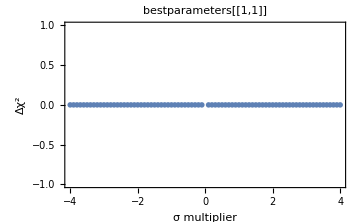
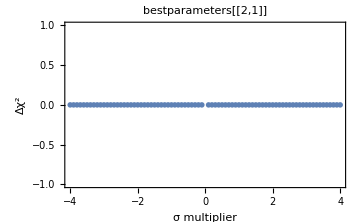
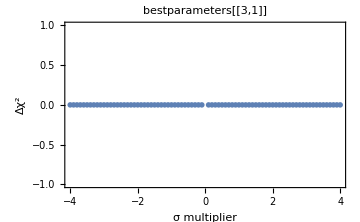

---------------------------------

```mathematica
kannblock3=Kann["060418_Kann.txt"];
liangdata=Liang["060418_Liang.txt",0.69,1.4901];

(*rescaling*)
(*Print[10^kannblock3[[1,2]]]
Print[10^sidata[[1,2]]]*)


rescalefactor=10^kannblock3[[6,2]]/10^liangdata[[4,2]];
(*don't change the second index, just change the first one*)
linearsi=rescalefactor*(10^liangdata[[All,2]]);
logsi=Log[10,linearsi];
newsi=Transpose[{liangdata[[All,1]]
,logsi}];
siwitherrs=Transpose[{10^liangdata[[All,1]],10^logsi,liangdata[[All,3]]}];
MatrixForm[siwitherrs]

(*SetDirectory["/Users/samanthalivermore/Desktop/comb_scratchwork"];
Export["041006_comb.txt",siwitherrs,"Table", "FieldSeparators"->"\t"];*)

kannplot=ListPlot[kannblock3,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->{Red},FrameLabel->{"log time (s)","log flux (erg cm-2 s-1)"}];
siplot=ListPlot[newsi,PlotRange->All,Frame->True,Axes->False,RotateLabel->True,PlotStyle->{Blue},FrameLabel->{"log time (s)","log flux (erg cm-2 s-1)"}];
Show[kannplot,siplot]

tt=2.2   (*start time of plateau, log scale*)
tf=7 (*end time of lightcurve, log scale*)
Dzielenie[tt,tf]
fitowanie[-12.82,4.8,1.5,0,ΔF1,Part1,tt,tf]   (*fitting: y,x coords of turning point/end of plateau*)
Chisquare[Part1,ΔF1]
IntervalEstimating[0.1,4,0.1,Part1,ΔF1]
```